```mathematica
(*Check on β2, which includes both YH and YF*)
```

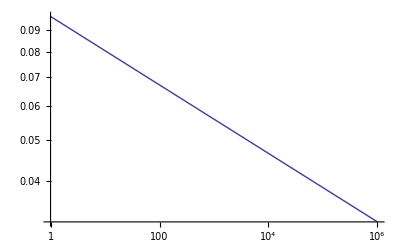

```mathematica
LogLogPlot[.0558*(x/1000)^0.92/(x/1000),{x,1,10^6}]
```

```mathematica
.0558*(x/1000)^0.92
```

0.0000969693 x^0.92

```mathematica
.0558*(1/1000)^.92
```

0.0000969693

```mathematica
1^.92
```

1.

```mathematica
.0558*(1)^0.92
.0558*(10^(4))^0.92
```

0.0558

267.076

```mathematica
10^(-1.5)
```

0.0316228

```mathematica
Ratesfunc[x_] :=(
ts=x[[1]];
M=x[[2]];
B0=x[[3]];
Em=x[[4]];
Emprime=x[[5]];
η=x[[6]];
λ0=x[[7]];
γ=x[[8]];
ζ=x[[9]];
f0=x[[10]];
mm0=x[[11]];
alpha=x[[12]];
Ed=x[[13]];
c=x[[14]];
k=x[[15]];
χ=x[[16]];

(*TimeScales*)
a = B0/Em;
aprime =  B0/Emprime;
ϵLam = 0.95;
m0 = .0558*(1/1000)^.92*M^0.92/1000;(*0.00001;*)
ϵSig = (1-f0*M^γ/M);
ϵMu = (1-(f0*M^γ+mm0*M^ζ)/M);
τLam = -Log[(1-ϵLam^(1/4))/(1 - (m0/M)^(1/4))]*(4*M^(1/4))/a;
τLamInvade = -Log[(1-(ϵLam*(1+χ))^(1/4))/(1 - (m0/(M*(1+χ)))^(1/4))]*(4*(M)^(1/4))/a;
τRhoStart = -Log[(1-(ϵSig*ϵLam)^(1/4))/(1 - (m0/M)^(1/4))]*(4*M^(1/4))/a;
τRhoStartInvade = -Log[(1-(ϵSig*ϵLam)^(1/4))/(1 - (m0/(M*(1+χ)))^(1/4))]*(4*(M)^(1/4))/a;
τRho = -Log[(1-ϵLam^(1/4))/(1-(ϵSig*ϵLam)^(1/4))]*(4*M^(1/4))/aprime;
τRhoInvade = -Log[(1-(ϵLam*(1+χ))^(1/4))/(1-(ϵSig*ϵLam)^(1/4))]*(4*(M)^(1/4))/aprime;
τSig = -M^(1/4)/aprime*Log[ϵSig];
τSigInvade =  -(M)^(1/4)/aprime*Log[ϵSig/(1+χ)];
τMu = -M^(1/4)/aprime*Log[ϵMu] -τSig;

(*BLam and Brho*)
BLam=1/(3 a)ⅇ^(-(a τLam)/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam)/M^(1/4))) m0+M (-48 ⅇ^((3 a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))-36 ⅇ^((a τLam)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2-16 ⅇ^((a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3+3 (-1+4 (m0/M)^(1/4)-6 √(m0/M)+4 (m0/M)^(3/4))+ⅇ^((a τLam)/M^(1/4)) (-25+12 (m0/M)^(1/4)+6 √(m0/M)+4 (m0/M)^(3/4)))+3 a ⅇ^((a τLam)/M^(1/4)) M^(3/4) τLam);
BRho=1/(3 a)M^(1/4) (ⅇ^(-(a τLam)/M^(1/4)) (-3 m0+M (-48 ⅇ^((3 a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))-36 ⅇ^((a τLam)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2-16 ⅇ^((a τLam)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3+3 (-1+4 (m0/M)^(1/4)-6 √(m0/M)+4 (m0/M)^(3/4)))+3 a ⅇ^((a τLam)/M^(1/4)) M^(3/4) τLam)+ⅇ^(-(a τRhoStart)/M^(1/4)) (3 m0+M (48 ⅇ^((3 a τRhoStart)/(4 M^(1/4))) (-1+(m0/M)^(1/4))+36 ⅇ^((a τRhoStart)/(2 M^(1/4))) (-1+(m0/M)^(1/4))^2+16 ⅇ^((a τRhoStart)/(4 M^(1/4))) (-1+(m0/M)^(1/4))^3+3 (1-4 (m0/M)^(1/4)+6 √(m0/M)-4 (m0/M)^(3/4)))-3 a ⅇ^((a τRhoStart)/M^(1/4)) M^(3/4) τRhoStart));
BLamInvade=1/(3 a)M^(1/4) (3 m0+M (1+χ) (-25+12 (m0/(M+M χ))^(1/4)+6 √(m0/(M+M χ))+4 (m0/(M+M χ))^(3/4))-ⅇ^(-(a τLamInvade)/M^(1/4)) (3 m0-3 a ⅇ^((a τLamInvade)/M^(1/4)) M^(3/4) τLamInvade (1+χ)+M (1+χ) (48 ⅇ^((3 a τLamInvade)/(4 M^(1/4))) (-1+(m0/(M+M χ))^(1/4))+36 ⅇ^((a τLamInvade)/(2 M^(1/4))) (-1+(m0/(M+M χ))^(1/4))^2+16 ⅇ^((a τLamInvade)/(4 M^(1/4))) (-1+(m0/(M+M χ))^(1/4))^3+3 (1-4 (m0/(M+M χ))^(1/4)+6 √(m0/(M+M χ))-4 (m0/(M+M χ))^(3/4)))));
BRhoInvade=1/(3 a)M^(1/4) (-ⅇ^(-(a τLamInvade)/M^(1/4)) (3 m0-3 a ⅇ^((a τLamInvade)/M^(1/4)) M^(3/4) τLamInvade (1+χ)+M (1+χ) (48 ⅇ^((3 a τLamInvade)/(4 M^(1/4))) (-1+(m0/(M+M χ))^(1/4))+36 ⅇ^((a τLamInvade)/(2 M^(1/4))) (-1+(m0/(M+M χ))^(1/4))^2+16 ⅇ^((a τLamInvade)/(4 M^(1/4))) (-1+(m0/(M+M χ))^(1/4))^3+3 (1-4 (m0/(M+M χ))^(1/4)+6 √(m0/(M+M χ))-4 (m0/(M+M χ))^(3/4))))+ⅇ^(-(a τRhoStartInvade)/M^(1/4)) (3 m0-3 a ⅇ^((a τRhoStartInvade)/M^(1/4)) M^(3/4) τRhoStartInvade (1+χ)+M (1+χ) (48 ⅇ^((3 a τRhoStartInvade)/(4 M^(1/4))) (-1+(m0/(M+M χ))^(1/4))+36 ⅇ^((a τRhoStartInvade)/(2 M^(1/4))) (-1+(m0/(M+M χ))^(1/4))^2+16 ⅇ^((a τRhoStartInvade)/(4 M^(1/4))) (-1+(m0/(M+M χ))^(1/4))^3+3 (1-4 (m0/(M+M χ))^(1/4)+6 √(m0/(M+M χ))-4 (m0/(M+M χ))^(3/4)))));

(*Yields for starving and full organisms*)
YF=M*Ed/BLam;
YH=M*Ed/BRho;
YFInvade=M*(1+χ)*Ed/BLamInvade;
YHInvade=M*(1+χ)*Ed/BRhoInvade;
(*Rates*)

ConsumerGrowth = ts*(Log[2]/τLam); (*Fecundity = 2*)
InvaderConsumerGrowth= ts*(Log[2]/τLamInvade); (*Fecundity = 2*)

Starvation = ts*(1/τSig);
InvaderStarvation = ts*(1/τSigInvade);

Mortality=ts*( 1/τMu);

Recovery = ts*(1/τRho);
InvaderRecovery= ts*(1/τRhoInvade);

PF=(B0*M^η)/M/Ed;
PH=PF;
PFInvade=(B0*(M*(1+χ))^η)/(M*(1+χ))/Ed;
PHInvade=PFInvade;

StarveMaintenance = ts*PH*(YH/(c/k));
FullMaintenance = ts*((ConsumerGrowth/YF+PF)*(YH/(c/k)));

InvaderStarveMaintenance = ts*PHInvade*(YHInvade/(c/k));
InvaderFullMaintenance = ts*((InvaderConsumerGrowth/YFInvade+PFInvade)*(YHInvade/(c/k)));
(*
StarveMaintenance = ts*((B0*M^η*YH)/(c/k*M*Ed));
FullMaintenance = ts*(YH*(ConsumerGrowth/YF+(B0*M^η))/(c/k));

InvaderStarveMaintenance = ts*((B0*(M*(1+χ))^η*YH)/(c/k*(M*(1+χ))*Ed));
InvaderFullMaintenance = ts*(YH*(ConsumerGrowth/YF+(B0*(M*(1+χ))^η))/(c/k));
*)
ResourceGrowth = ts*alpha;

{ConsumerGrowth,Starvation,Mortality,Recovery,StarveMaintenance,FullMaintenance,ResourceGrowth,InvaderConsumerGrowth,InvaderStarvation,InvaderRecovery,InvaderStarveMaintenance,InvaderFullMaintenance,YH,YF,k,YHInvade}
);
```

```mathematica
parameters={
(*ts*)1,
(*M*)M,
(*B0*)4.7*10^(-2),
(*Em*)5774(*J/gram*),
(*Emprime*)7000 (*10000*),
(*η*)3/4,
(*λ0*)3.39*10^(-7),
(*γ*)1.19,
(*ζ*)1.00,
(*f0*)0.0202,
(*mm0*)0.383,
(*α*)(*2.10*10^(-9)*)9.45*^-9,
(*Ed*)18200,
(*c*)(*5*)23000,
(*k*)(*10*)23000/2,
(*χ*)chi};
RF =Ratesfunc[parameters];
```

```mathematica
dimSS[ndSS_]:=(
ndSS*YH*k
);
dimSSInvader[ndSS_]:=(
ndSS*YHInvade*k
);
dimRSS[ndR_]:=(
ndR*c
);
```

```mathematica
dF =λ*F-σ*(1-R)*F +ρ*c/k* R * H;
dH =σ*(1-R)*F - ρ*c/k* R*H - μ*H;
dR =α*R*(1-R) -ρ*H*R -δ*H- β*F;
SteadyStateSol = FullSimplify[Solve[
{
0 ==dF,
0==dH,
0 ==dR 
},{F,H,R}]
]
FSS = F/.SteadyStateSol[[3]]
HSS = H/.SteadyStateSol[[3]]
RSS = R/.SteadyStateSol[[3]]
```

{{F→0,H→0,R→0},{F→0,H→0,R→1},{F→-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ)),H→-(α λ^2 μ (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ)),R→(μ (-λ+σ))/(2 λ ρ+μ σ)}}

-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

-(α λ^2 μ (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

(μ (-λ+σ))/(2 λ ρ+μ σ)

```mathematica
{InvaderStarvation,InvaderRecovery,InvaderStarveMaintenance,InvaderFullMaintenance}
```

{-(6.71429×10^-6)/(M^(1/4) Log[(1-0.0202 M^0.19)/(1+chi)]),-(1.67857×10^-6)/(M^(1/4) Log[(1-0.987259 (1+chi)^(1/4))/(1-0.987259 (1-0.0202 M^0.19)^(1/4))]),(5.73866×10^-7 ((1+chi) M)^(3/4))/(M^(1/4) (-((1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^4. (2.90908×10^-7 M^0.92+(1+chi) M ((48 (-1+0.0176465 (M^0.92/(M+chi M))^(1/4)))/(((1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^3.)+(36 (-1+0.0176465 (M^0.92/(M+chi M))^(1/4))^2)/(((1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^2.)+(16 (-1+0.0176465 (M^0.92/(M+chi M))^(1/4))^3)/(((1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^1.)+3 (1-0.070586 (M^0.92/(M+chi M))^(1/4)+0.00186839 √(M^0.92/(M+chi M))-0.0000219804 (M^0.92/(M+chi M))^(3/4)))+(12. (1+chi) M Log[(1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4))])/(((1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^4. (2.90908×10^-7 M^0.92+(1+chi) M ((48 (-1+0.0176465 (M^0.92/(M+chi M))^(1/4)))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^3.)+(36 (-1+0.0176465 (M^0.92/(M+chi M))^(1/4))^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^2.)+(16 (-1+0.0176465 (M^0.92/(M+chi M))^(1/4))^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^1.)+3 (1-0.070586 (M^0.92/(M+chi M))^(1/4)+0.00186839 √(M^0.92/(M+chi M))-0.0000219804 (M^0.92/(M+chi M))^(3/4)))+(12. (1+chi) M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4))])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^4.)))),(0.22222 (1+chi) M^(3/4) ((2.58242×10^-6 ((1+chi) M)^(3/4))/((1+chi) M)-1/((1+chi) M Log[(1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4))])3.17375×10^-6 (2.90908×10^-7 M^0.92+(1+chi) M (-25+0.211758 (M^0.92/(M+chi M))^(1/4)+0.00186839 √(M^0.92/(M+chi M))+0.0000219804 (M^0.92/(M+chi M))^(3/4))-((1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^4. (2.90908×10^-7 M^0.92+(1+chi) M ((48 (-1+0.0176465 (M^0.92/(M+chi M))^(1/4)))/(((1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^3.)+(36 (-1+0.0176465 (M^0.92/(M+chi M))^(1/4))^2)/(((1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^2.)+(16 (-1+0.0176465 (M^0.92/(M+chi M))^(1/4))^3)/(((1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^1.)+3 (1-0.070586 (M^0.92/(M+chi M))^(1/4)+0.00186839 √(M^0.92/(M+chi M))-0.0000219804 (M^0.92/(M+chi M))^(3/4)))+(12. (1+chi) M Log[(1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4))])/(((1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^4.)))))/(-((1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^4. (2.90908×10^-7 M^0.92+(1+chi) M ((48 (-1+0.0176465 (M^0.92/(M+chi M))^(1/4)))/(((1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^3.)+(36 (-1+0.0176465 (M^0.92/(M+chi M))^(1/4))^2)/(((1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^2.)+(16 (-1+0.0176465 (M^0.92/(M+chi M))^(1/4))^3)/(((1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^1.)+3 (1-0.070586 (M^0.92/(M+chi M))^(1/4)+0.00186839 √(M^0.92/(M+chi M))-0.0000219804 (M^0.92/(M+chi M))^(3/4)))+(12. (1+chi) M Log[(1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4))])/(((1-0.987259 (1+chi)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^4. (2.90908×10^-7 M^0.92+(1+chi) M ((48 (-1+0.0176465 (M^0.92/(M+chi M))^(1/4)))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^3.)+(36 (-1+0.0176465 (M^0.92/(M+chi M))^(1/4))^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^2.)+(16 (-1+0.0176465 (M^0.92/(M+chi M))^(1/4))^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^1.)+3 (1-0.070586 (M^0.92/(M+chi M))^(1/4)+0.00186839 √(M^0.92/(M+chi M))-0.0000219804 (M^0.92/(M+chi M))^(3/4)))+(12. (1+chi) M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4))])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465 (1/((1+chi) M^0.08))^(1/4)))^4.)))}